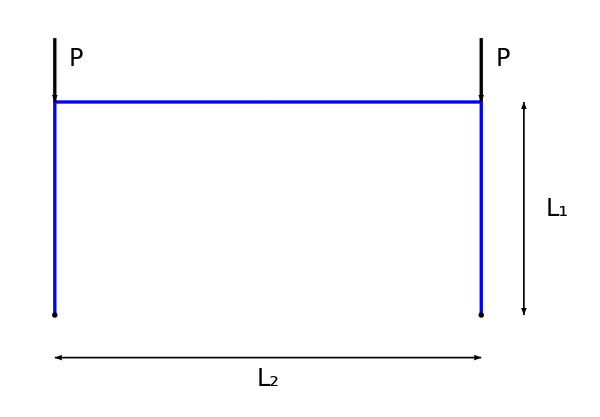
-Graphics-Symmetric portal

```mathematica
Module[{},
L=1;
L1 = L;
L2 = L;
L3 = L2;
α1=90 Degree;
α2 = 0;

xA = {0,0};
xB = {L1*Cos[α1], L1*Sin[α1]};
xC = xB + {L2*Cos[α2], L2*Sin[α2]};
xD = xC + {L3*Cos[α2], -L3*Sin[α2]};
xE = xD + {L1*Cos[α1], -L1*Sin[α1]};

myCircle[o_,r_,{a_,b_},res_]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];

cer={Disk[{0,0},0.06],Gray,Triangle[{{-0.5,-0.5},{0,0},{0.5,-0.5}}]};
app={Disk[{0,0},0.06],Gray,Triangle[{{-0.5,-0.5},{0,0},{0.5,-0.5}}],Disk[{-0.25,-0.5},0.1],Disk[{0.25,-0.5},0.1]};
inc={Disk[{0,0},0.06],Thickness[0.06],Line[{{0,0},{0,-0.1}}],Gray,Rectangle[{-0.5,-0.6},{0.5,-0.1}]};
pat={Disk[{0,0},0.05],Thickness[0.04],Line[{{-0.5,0.1},{-0.4,0},{0.4,0},{0.5,0.1}}],Gray,Rectangle[{-0.5,-0.6},{0.5,-0.1}]};


Labeled[
Show[{
Graphics[{Blue,Thickness[0.004],Line[{xA,xB}],Line[{xB,xC}],Line[{xC,xD}], Line[{xD, xE}]}],
Graphics[{Inset[Graphics@inc,xA,{0,0},Scaled[0.08]]}],
Graphics[{Inset[Graphics@inc,xE,{0,0},Scaled[0.08]]}],
Graphics[{Thickness[0.002],Arrowheads[{-0.02,0.02}],Arrow[{xA+{0,-0.2},xE+{0,-0.2}}]}],
Graphics[{Text[Style["L_2",24],(xA+xE)/2+{0,-0.3}]}],
Graphics[{Thickness[0.002],Arrowheads[{-0.02,0.02}],Arrow[{xD+{0.2,0},xE+{0.2,0}}]}],
Graphics[{Text[Style["L_1",24],(xD+xE)/2+{0.3,0},{-1,0}]}],
Graphics[{Thickness[0.004],Arrowheads[0.03],Arrow[{xB+{0,0.3},xB+{0,0}}],Arrow[{xD+{0,0.3},xD+{0,0}}]}],
Graphics[{Text[Style["P",24],xB+{0.1,0.2}],Text[Style["P",24],xD+{0.1,0.2}]}]
},Axes->False,AspectRatio->Automatic,ImageSize->600]
,Style["Symmetric portal",24],Top]
]
```

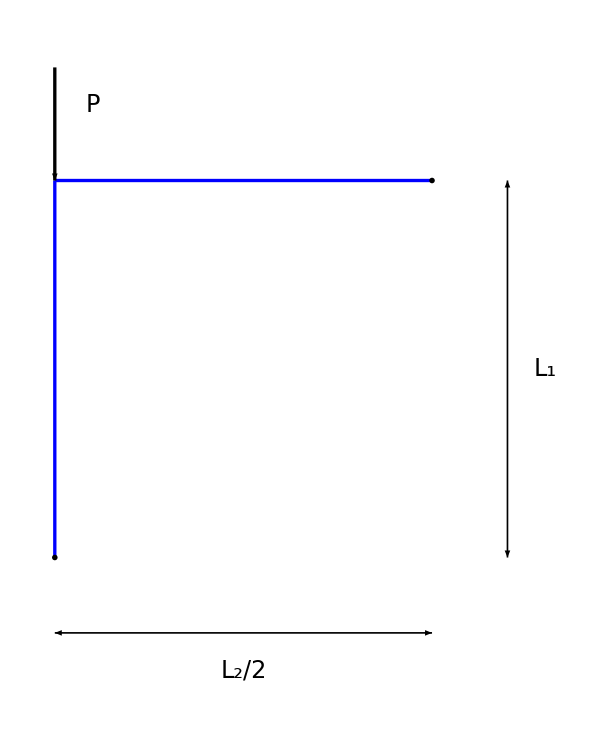
-Graphics-Symmetric mode

```mathematica
Module[{},
L=1;
L1 = L;
L2 = L;
L3 = L2;
α1=90 Degree;
α2 = 0;

xA = {0,0};
xB = {L1*Cos[α1], L1*Sin[α1]};
xC = xB + {L2*Cos[α2], L2*Sin[α2]};
xD = xC + {L3*Cos[α2], -L3*Sin[α2]};
xE = xD + {L1*Cos[α1], -L1*Sin[α1]};

myCircle[o_,r_,{a_,b_},res_]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];

cer={Disk[{0,0},0.06],Gray,Triangle[{{-0.5,-0.5},{0,0},{0.5,-0.5}}]};
app={Disk[{0,0},0.06],Gray,Triangle[{{-0.5,-0.5},{0,0},{0.5,-0.5}}],Disk[{-0.25,-0.5},0.1],Disk[{0.25,-0.5},0.1]};
inc={Disk[{0,0},0.06],Thickness[0.06],Line[{{0,0},{0,-0.1}}],Gray,Rectangle[{-0.5,-0.6},{0.5,-0.1}]};
pat={Disk[{0,0},0.05],Thickness[0.04],Line[{{-0.5,0.1},{-0.4,0},{0.4,0},{0.5,0.1}}],Gray,Rectangle[{-0.5,-0.6},{0.5,-0.1}]};


Labeled[
Show[{
Graphics[{Blue,Thickness[0.004],Line[{xA,xB}],Line[{xB,xC}]}],
Graphics[{Inset[Graphics@inc,xA,{0,0},Scaled[0.08]]}],
Graphics[{Inset[Graphics@pat,xC,{0,0},Scaled[0.08],{0,1}]}],
Graphics[{Thickness[0.002],Arrowheads[{-0.02,0.02}],Arrow[{xA+{0,-0.2},xE/2+{0,-0.2}}]}],
Graphics[{Text[Style["L_2/2",24],(xA+xE/2)/2+{0,-0.3}]}],
Graphics[{Thickness[0.002],Arrowheads[{-0.02,0.02}],Arrow[{xC+{0.2,0},(xE-xA)/2+{0.2,0}}]}],
Graphics[{Text[Style["L_1",24],(xC-(xA-xE)/2)/2+{.3,0},{0,0} ]}],
Graphics[{Thickness[0.004],Arrowheads[0.03],Arrow[{xB+{0,0.3},xB+{0,0}}]}],
Graphics[{Text[Style["P",24],xB+{0.1,0.2}]}]
},Axes->False,AspectRatio->Automatic,ImageSize->600]
,Style["Symmetric mode",24],Top]
]
```

```mathematica
Module[{},
L=1;
L1 = L;
L2 = L;
L3 = L2;
α1=90 Degree;
α2 = 0;

xA = {0,0};
xB = {L1*Cos[α1], L1*Sin[α1]};
xC = xB + {L2*Cos[α2], L2*Sin[α2]};
xD = xC + {L3*Cos[α2], -L3*Sin[α2]};
xE = xD + {L1*Cos[α1], -L1*Sin[α1]};

myCircle[o_,r_,{a_,b_},res_]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];

cer={Disk[{0,0},0.06],Gray,Triangle[{{-0.5,-0.5},{0,0},{0.5,-0.5}}]};
app={Disk[{0,0},0.06],Gray,Triangle[{{-0.5,-0.5},{0,0},{0.5,-0.5}}],Disk[{-0.25,-0.5},0.1],Disk[{0.25,-0.5},0.1]};
inc={Disk[{0,0},0.06],Thickness[0.06],Line[{{0,0},{0,-0.1}}],Gray,Rectangle[{-0.5,-0.6},{0.5,-0.1}]};
pat={Disk[{0,0},0.05],Thickness[0.04],Line[{{-0.5,0.1},{-0.4,0},{0.4,0},{0.5,0.1}}],Gray,Rectangle[{-0.5,-0.6},{0.5,-0.1}]};


Labeled[
Show[{
Graphics[{Blue,Thickness[0.004],Line[{xA,xB}],Line[{xB,xC}]}],
Graphics[{Inset[Graphics@inc,xA,{0,0},Scaled[0.08]]}],
Graphics[{Inset[Graphics@app,xC,{0,0},Scaled[0.08]]}],
Graphics[{Thickness[0.002],Arrowheads[{-0.02,0.02}],Arrow[{xA+{0,-0.2},xE/2+{0,-0.2}}]}],
Graphics[{Text[Style["L_2/2",24],(xA+xE/2)/2+{0,-0.3}]}],
Graphics[{Thickness[0.002],Arrowheads[{-0.02,0.02}],Arrow[{xC+{0.2,0},(xE-xA)/2+{0.2,0}}]}],
Graphics[{Text[Style["L_1",24],(xC-(xA-xE)/2)/2+{.3,0},{0,0} ]}],
Graphics[{Thickness[0.004],Arrowheads[0.03],Arrow[{xB+{0,0.3},xB+{0,0}}]}],
Graphics[{Text[Style["P",24],xB+{0.1,0.2}]}]
},Axes->False,AspectRatio->Automatic,ImageSize->600]
,Style["Anti-symmetric mode",24],Top]
]
```

-Graphics-Anti-symmetric mode

# Analytic solution

## Symmetric mode

## Column only

```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s]+c4*Sin[α*s];
(*
α = √(P/EJ1);
ϕ = k/(EJ1/l1)=(EJ2/l1)/(EJ1/l1)=EJ2/EJ1 ;
*)
EJ1 = 1;
EJ2 = 8;

ϕ = EJ2/EJ1;

l1 = 1;
l2 = 2*l1;

{RR, MM} = CoefficientArrays[
{
v[0]==0,
v'[0]==0,
v[l1]==0,
-(v''[l1]) == ϕ/l1*v'[l1]
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
1 | 1 | Cos[α] | Sin[α]
0 | -8 | α^2 Cos[α]+8 α Sin[α] | -8 α Cos[α]+α^2 Sin[α])

(0
0
0
0)

```mathematica
detM[α_] = Det[MM]//Simplify
```

α (-16+(16+α^2) Cos[α]+7 α Sin[α])

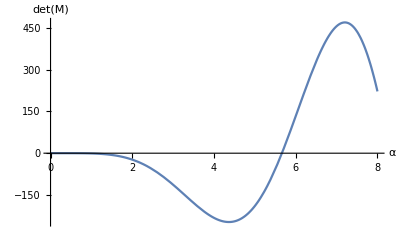

```mathematica
Plot[detM[α], {α, 0, 8}, AxesLabel->{"α", "det(M)"}]
```

### P_(cr,1)

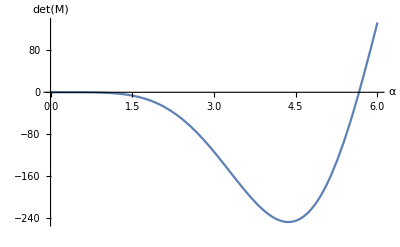

```mathematica
Plot[detM[α], {α, 0, 6}, AxesLabel->{"α", "det(M)"}]
```

```mathematica
αcr = α/.FindRoot[detM[α]==0, {α, 6}]
```

5.66179

```mathematica
Pcr = αcr^2*EJ1/l1^2/.EJ1->1
```

32.0559

```mathematica
Mcr = MM/.α->αcr//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 5.66179
1 | 1 | 0.813069 | -0.582167
0 | -8 | -0.305216 | -55.4893)

```mathematica
Eigensystem[Mcr]//Chop
```

{{-54.6796,1.90361,0.0997411,0},{{-0.000220244,-0.101156,0.0122631,0.994795},{0.741907,-0.0119241,0.670394,-0.00190306},{-0.721606,0.236329,0.649632,-0.0375777},{-0.701927,0.118978,0.701927,-0.0210142}}}

```mathematica
{c1, c2, c3, c4} = Eigenvectors[Mcr]//Chop//Last
v[s]
```

{-0.701927,0.118978,0.701927,-0.0210142}

-0.701927+0.118978 s+0.701927 Cos[s α]-0.0210142 Sin[s α]

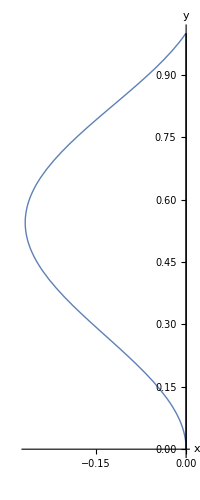

```mathematica
v1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

fact=0.2;
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,-fact*v[x]/.α->.999*αcr}],{x,0,l1},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef}]
```

### P_(cr,2)

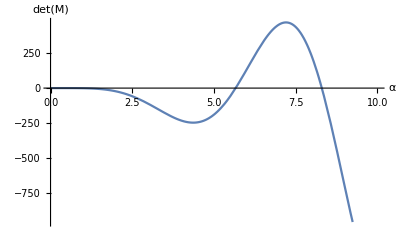

```mathematica
Plot[detM[α], {α, 0, 10}, AxesLabel->{"α", "det(M)"}]
```

```mathematica
αcr = α/.FindRoot[detM[α]==0, {α, 8}]
```

8.29801

```mathematica
Pcr = αcr^2*EJ1/l1^2/.EJ1->1
```

68.857

```mathematica
Mcr = MM/.α->αcr//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 8.29801
1 | 1 | -0.429585 | 0.903027
0 | -8 | 30.3667 | 90.6973)

```mathematica
Eigensystem[Mcr]//Chop
```

{{90.2873,0.990237+0.862203 ⅈ,0.990237-0.862203 ⅈ,0},{{0.000122441,0.0925318,0.0109324,0.99565},{-0.304326-0.255752 ⅈ,0.84661,0.223482-0.259894 ⅈ,-0.000996114+0.0879668 ⅈ},{-0.304326+0.255752 ⅈ,0.84661,0.223482+0.259894 ⅈ,-0.000996114-0.0879668 ⅈ},{0.465712,-0.747074,-0.465712,0.0900305}}}

```mathematica
{c1, c2, c3, c4} = Eigenvectors[Mcr]//Chop//Last
v[s]
```

{0.465712,-0.747074,-0.465712,0.0900305}

0.465712-0.747074 s-0.465712 Cos[s α]+0.0900305 Sin[s α]

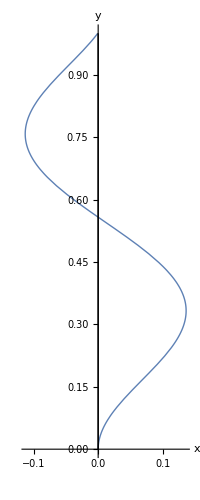

```mathematica
v1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

fact=0.2;
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,-fact*v[x]/.α->.999*αcr}],{x,0,l1},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef}]
```

### P_(cr,3)

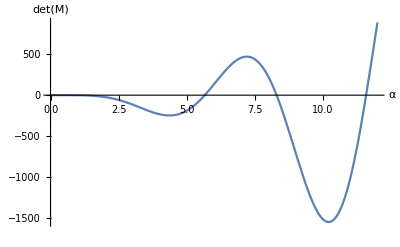

```mathematica
Plot[detM[α], {α, 0, 12}, AxesLabel->{"α", "det(M)"}]
```

```mathematica
αcr = α/.FindRoot[detM[α]==0, {α, 12}]
```

11.5845

```mathematica
Pcr = αcr^2*EJ1/l1^2/.EJ1->1
```

134.201

```mathematica
Mcr = MM/.α->αcr//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 11.5845
1 | 1 | 0.555463 | -0.831541
0 | -8 | -2.5204 | -163.071)

```mathematica
Eigensystem[Mcr]//Chop
```

{{-162.519,1.75416,0.248488,0},{{-0.000033757,-0.070667,0.00551989,0.997485},{0.795784,-0.0807576,0.600149,-0.0052574},{-0.690097,0.503722,0.518616,-0.0326776},{-0.678327,0.281346,0.678327,-0.0242864}}}

```mathematica
{c1, c2, c3, c4} = Eigenvectors[Mcr]//Chop//Last
v[s]
```

{-0.678327,0.281346,0.678327,-0.0242864}

-0.678327+0.281346 s+0.678327 Cos[s α]-0.0242864 Sin[s α]

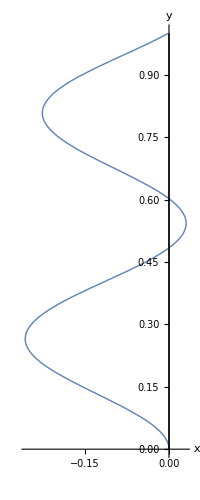

```mathematica
v1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

fact=0.2;
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,-fact*v[x]/.α->.999*αcr}],{x,0,l1},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef}]
```

## Frame

```mathematica
ClearAll["Global`*"]

v1[s1_] = c1+c2*s1+c3*Cos[α1*s1]+c4*Sin[α1*s1];
v2[s2_] = c5+c6*s2+c7*s2^2+c8*s2^3;

(*
α1 = √(P1/EJ1);
α2 = √(P2/EJ2);
ϕ = k/(EJ1/l1)=(EJ2/l1)/(EJ1/l1)=EJ2/EJ1 ;
*)
EJ1 = 1;
EJ2 = 8;

ϕ = EJ2/EJ1;

l1 = 1;
l2 = 2*l1;

{RR, MM} = CoefficientArrays[
{
v1[0] == 0, 
v1'[0]==0,
v2'[l2/2]==0,
-(v2'''[l2/2]+α2^2*v2'[l2/2])==0,
v1'[l1]==v2'[0],
-(v1''[l1])==-ϕ*v2''[0],
v1[l1]==0,
v2[0]==0
},
{c1,c2,c3,c4,c5,c6,c7,c8}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | α1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 3
0 | 0 | 0 | 0 | 0 | -α2^2 | -2 α2^2 | -6-3 α2^2
0 | 1 | -α1 Sin[α1] | α1 Cos[α1] | 0 | -1 | 0 | 0
0 | 0 | α1^2 Cos[α1] | α1^2 Sin[α1] | 0 | 0 | 16 | 0
1 | 1 | Cos[α1] | Sin[α1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(0
0
0
0
0
0
0
0)

```mathematica
detM[α1_, α2_] = Det[MM]//Simplify;
detM[α1, 0]
```

12 α1 (-16+(16+α1^2) Cos[α1]+7 α1 Sin[α1])

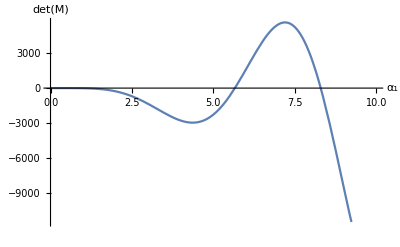

```mathematica
Plot[detM[α1, 0], {α1, 0, 10}, AxesLabel->{"α_1", "det(M)"}]
```

### P_(cr,1)

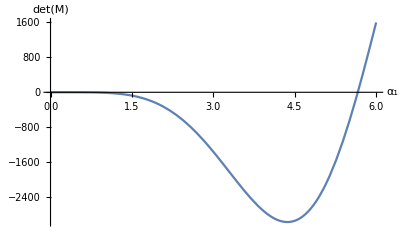

```mathematica
Plot[detM[α1, 0], {α1, 0, 6}, AxesLabel->{"α_1", "det(M)"}]
```

```mathematica
α1cr  = α1/.FindRoot[detM[α1, 0]==0, {α1, 6}]
```

5.66179

```mathematica
P1cr = α1cr^2*EJ1/l1^2/.EJ1->1
```

32.0559

```mathematica
Mcr = MM/.{α1->α1cr, α2->0};
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 5.66179 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | -6
0 | 1 | 3.29611 | 4.60343 | 0 | -1 | 0 | 0
0 | 0 | 26.0637 | -18.6619 | 0 | 0 | 16 | 0
1 | 1 | 0.813069 | -0.582167 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
Eigensystem[Mcr]//Chop
```

{{5.42794,-4.22876+1.53316 ⅈ,-4.22876-1.53316 ⅈ,2.32564+2.67453 ⅈ,2.32564-2.67453 ⅈ,0.557233,-0.17892,0},{{0.042604,0.0140265,0.188648,0.0109697,-0.053866,0.97871,0.0375148,-0.00992384},{0.0328788+0.0107383 ⅈ,0.000779689+0.116558 ⅈ,-0.188379-0.00573945 ⅈ,-0.0322828-0.107432 ⅈ,0.315742+0.208335 ⅈ,0.885861,0.0350807-0.0310701 ⅈ,-0.0502044-0.0674681 ⅈ},{0.0328788-0.0107383 ⅈ,0.000779689-0.116558 ⅈ,-0.188379+0.00573945 ⅈ,-0.0322828+0.107432 ⅈ,0.315742-0.208335 ⅈ,0.885861,0.0350807+0.0310701 ⅈ,-0.0502044+0.0674681 ⅈ},{-0.00321146+0.045253 ⅈ,0.292559+0.17285 ⅈ,-0.125288+0.0514 ⅈ,-0.0131522+0.17867 ⅈ,0.366618+0.0792182 ⅈ,-0.821699,0.0693153-0.0126879 ⅈ,0.0847411-0.063391 ⅈ},{-0.00321146-0.045253 ⅈ,0.292559-0.17285 ⅈ,-0.125288-0.0514 ⅈ,-0.0131522-0.17867 ⅈ,0.366618-0.0792182 ⅈ,-0.821699,0.0693153+0.0126879 ⅈ,0.0847411+0.063391 ⅈ},{-0.479945,0.117958,0.212504,-0.00922462,0.000477387,0.775664,-0.32991,0.000856711},{0.213396,-0.0777868,-0.251577,0.0161971,-0.0000864173,-0.832467,0.438015,0.000482995},{-0.251003,0.0425455,0.251003,-0.00751449,0,0.835286,-0.417643,0}}}

```mathematica
{c1,c2,c3,c4,c5,c6,c7,c8}=Eigenvectors[Mcr]//Chop//Last
v1[s1]
v2[s2]
```

{-0.251003,0.0425455,0.251003,-0.00751449,0,0.835286,-0.417643,0}

-0.251003+0.0425455 s1+0.251003 Cos[s1 α1]-0.00751449 Sin[s1 α1]

0.835286 s2-0.417643 s2^2

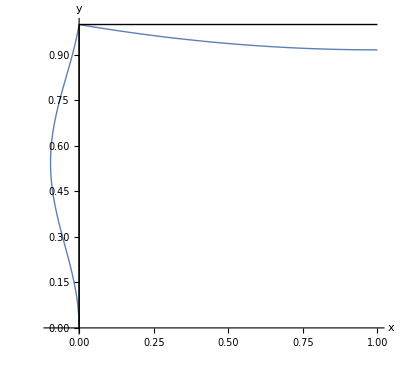

```mathematica
vv1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

vv2 = {0,l1};
θ2 = 0;
T2 = RotationMatrix[θ2];

fact=0.2;
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]],ParametricPlot[AffineTransform[{T2,vv2}][{x,0}],{x,0,l2/2},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,-fact*v1[x]/.α1->.999*α1cr}],{x,0,l1},PlotStyle->Thick],
ParametricPlot[AffineTransform[{T2,vv2}][{x,-fact*v2[x]}],{x,0,l2/2},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef},PlotRange->All]
```

### P_(cr,2)

```mathematica
Plot[detM[α1, 0], {α1, 0, 10}, AxesLabel->{"α_1", "det(M)"}]
```

-Graphics-

```mathematica
α1cr  = α1/.FindRoot[detM[α1, 0]==0, {α1, 8}]
```

8.29801

```mathematica
P1cr = α1cr^2*EJ1/l1^2/.EJ1->1
```

68.857

```mathematica
Mcr = MM/.{α1->α1cr, α2->0};
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 8.29801 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | -6
0 | 1 | -7.49333 | -3.5647 | 0 | -1 | 0 | 0
0 | 0 | -29.5799 | 62.1797 | 0 | 0 | 16 | 0
1 | 1 | -0.429585 | 0.903027 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
Eigensystem[Mcr]//Chop
```

{{0.760058+6.64543 ⅈ,0.760058-6.64543 ⅈ,4.76885,-3.0659+2.69348 ⅈ,-3.0659-2.69348 ⅈ,0.921422+0.468933 ⅈ,0.921422-0.468933 ⅈ,0},{{-0.0240034-0.00057986 ⅈ,0.0330807-0.0179008 ⅈ,0.00961283-0.159374 ⅈ,0.0133792+0.0270101 ⅈ,0.142662+0.173676 ⅈ,0.959079,0.0113367-0.00126598 ⅈ,0.0282209-0.01824 ⅈ},{-0.0240034+0.00057986 ⅈ,0.0330807+0.0179008 ⅈ,0.00961283+0.159374 ⅈ,0.0133792-0.0270101 ⅈ,0.142662-0.173676 ⅈ,0.959079,0.0113367+0.00126598 ⅈ,0.0282209+0.01824 ⅈ},{-0.0388398,-0.254266,-0.146381,-0.115484,0.437722,-0.833145,-0.0701444,0.0917878},{0.00843961+0.0365306 ⅈ,0.150374+0.112987 ⅈ,-0.132709-0.125798 ⅈ,-0.110356-0.00655159 ⅈ,0.0574852-0.301429 ⅈ,0.902543,0.0105786-0.055171 ⅈ,-0.0593311+0.0461924 ⅈ},{0.00843961-0.0365306 ⅈ,0.150374-0.112987 ⅈ,-0.132709+0.125798 ⅈ,-0.110356+0.00655159 ⅈ,0.0574852+0.301429 ⅈ,0.902543,0.0105786+0.055171 ⅈ,-0.0593311-0.0461924 ⅈ},{-0.0899617+0.304596 ⅈ,-0.287752-0.540903 ⅈ,-0.135766-0.0661207 ⅈ,0.0332921-0.0111392 ⅈ,-0.00509515-0.00362702 ⅈ,0.613906,-0.345024-0.0609582 ⅈ,-0.00598327-0.000891308 ⅈ},{-0.0899617-0.304596 ⅈ,-0.287752+0.540903 ⅈ,-0.135766+0.0661207 ⅈ,0.0332921+0.0111392 ⅈ,-0.00509515+0.00362702 ⅈ,0.613906,-0.345024+0.0609582 ⅈ,-0.00598327+0.000891308 ⅈ},{0.16135,-0.258831,-0.16135,0.031192,0,0.839031,-0.419515,0}}}

```mathematica
{c1,c2,c3,c4,c5,c6,c7,c8}=Eigenvectors[Mcr]//Chop//Last
v1[s1]
v2[s2]
```

{0.16135,-0.258831,-0.16135,0.031192,0,0.839031,-0.419515,0}

0.16135-0.258831 s1-0.16135 Cos[s1 α1]+0.031192 Sin[s1 α1]

0.839031 s2-0.419515 s2^2

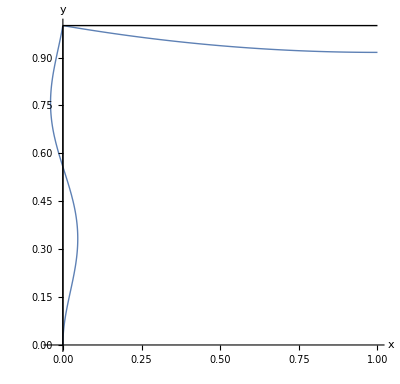

```mathematica
vv1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

vv2 = {0,l1};
θ2 = 0;
T2 = RotationMatrix[θ2];

fact=0.2;
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]],ParametricPlot[AffineTransform[{T2,vv2}][{x,0}],{x,0,l2/2},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,-fact*v1[x]/.α1->.999*α1cr}],{x,0,l1},PlotStyle->Thick],
ParametricPlot[AffineTransform[{T2,vv2}][{x,-fact*v2[x]}],{x,0,l2/2},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef},PlotRange->All]
```

### P_(cr,3)

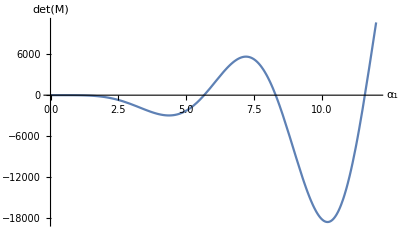

```mathematica
Plot[detM[α1, 0], {α1, 0, 12}, AxesLabel->{"α_1", "det(M)"}]
```

```mathematica
α1cr  = α1/.FindRoot[detM[α1, 0]==0, {α1, 12}]
```

11.5845

```mathematica
P1cr = α1cr^2*EJ1/l1^2/.EJ1->1
```

134.201

```mathematica
Mcr = MM/.{α1->α1cr, α2->0};
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 11.5845 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | -6
0 | 1 | 9.63298 | 6.43476 | 0 | -1 | 0 | 0
0 | 0 | 74.5435 | -111.593 | 0 | 0 | 16 | 0
1 | 1 | 0.555463 | -0.831541 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
Eigensystem[Mcr]//Chop
```

{{8.84937,-6.87499+1.94791 ⅈ,-6.87499-1.94791 ⅈ,2.79676+3.76862 ⅈ,2.79676-3.76862 ⅈ,0.653538+0.137526 ⅈ,0.653538-0.137526 ⅈ,0},{{-0.0146086,0.00133239,-0.114669,0.000902796,-0.0117832,-0.993185,-0.00878268,-0.00133153},{-0.0136018-0.0057508 ⅈ,-0.0179623-0.04887 ⅈ,0.118316+0.0187925 ⅈ,0.0204279+0.0302008 ⅈ,-0.282819-0.127622 ⅈ,-0.93975,-0.00495538+0.00867534 ⅈ,0.0332117+0.0279731 ⅈ},{-0.0136018+0.0057508 ⅈ,-0.0179623+0.04887 ⅈ,0.118316-0.0187925 ⅈ,0.0204279-0.0302008 ⅈ,-0.282819+0.127622 ⅈ,-0.93975,-0.00495538-0.00867534 ⅈ,0.0332117-0.0279731 ⅈ},{-0.0100675-0.0279423 ⅈ,-0.186136-0.17633 ⅈ,0.0872149-0.0881463 ⅈ,0.0284932-0.0879021 ⅈ,-0.278527-0.193584 ⅈ,0.886781,-0.0525959+0.00646231 ⅈ,-0.0684931+0.0230769 ⅈ},{-0.0100675+0.0279423 ⅈ,-0.186136+0.17633 ⅈ,0.0872149+0.0881463 ⅈ,0.0284932+0.0879021 ⅈ,-0.278527+0.193584 ⅈ,0.886781,-0.0525959-0.00646231 ⅈ,-0.0684931-0.0230769 ⅈ},{0.243304+0.0892265 ⅈ,0.072612-0.0372869 ⅈ,-0.0965664+0.00254693 ⅈ,-0.00172898+0.00197717 ⅈ,0.000176863-0.0000827136 ⅈ,-0.868863,0.402351-0.00554433 ⅈ,0.000233645-0.000175729 ⅈ},{0.243304-0.0892265 ⅈ,0.072612+0.0372869 ⅈ,-0.0965664-0.00254693 ⅈ,-0.00172898-0.00197717 ⅈ,0.000176863+0.0000827136 ⅈ,-0.868863,0.402351+0.00554433 ⅈ,0.000233645+0.000175729 ⅈ},{-0.0902959,0.0374515,0.0902959,-0.0032329,0,0.886467,-0.443234,0}}}

```mathematica
{c1,c2,c3,c4,c5,c6,c7,c8}=Eigenvectors[Mcr]//Chop//Last
v1[s1]
v2[s2]
```

{-0.0902959,0.0374515,0.0902959,-0.0032329,0,0.886467,-0.443234,0}

-0.0902959+0.0374515 s1+0.0902959 Cos[s1 α1]-0.0032329 Sin[s1 α1]

0.886467 s2-0.443234 s2^2

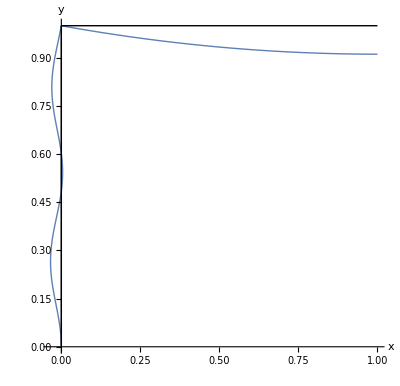

```mathematica
vv1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

vv2 = {0,l1};
θ2 = 0;
T2 = RotationMatrix[θ2];

fact=0.2;
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]],ParametricPlot[AffineTransform[{T2,vv2}][{x,0}],{x,0,l2/2},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,-fact*v1[x]/.α1->.999*α1cr}],{x,0,l1},PlotStyle->Thick],
ParametricPlot[AffineTransform[{T2,vv2}][{x,-fact*v2[x]}],{x,0,l2/2},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef},PlotRange->All]
```

## Anti-symmetric mode

## Column only

```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s]+c4*Sin[α*s];
(*
α = √(P/EJ1);
ϕ = k/(EJ1/l1)=(EJ2/l1)/(EJ1/l1)=EJ2/EJ1 ;
*)
EJ2 = 8;
EJ1 = 1;

ϕ = 3*EJ2/EJ1;

l1 = 1;
l2 = 2*l1;

{RR, MM} = CoefficientArrays[
{
v[0]==0,
v'[0]==0,
-(v''[l1]) == ϕ/l1*v'[l1],
-(v'''[l1]+α^2*v'[l1])==0
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
0 | -24 | α^2 Cos[α]+24 α Sin[α] | -24 α Cos[α]+α^2 Sin[α]
0 | -α^2 | 0 | 0)

(0
0
0
0)

```mathematica
detM[α_] = Det[MM]//Simplify
```

α^4 (α Cos[α]+24 Sin[α])

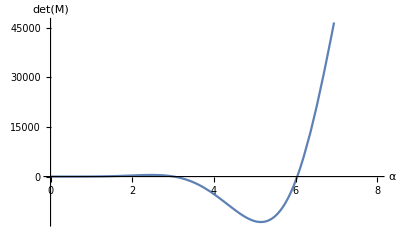

```mathematica
Plot[detM[α], {α, 0, 8}, AxesLabel->{"α", "det(M)"}]
```

### P_(cr,1)

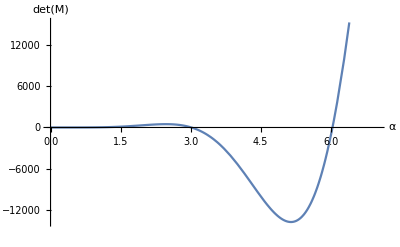

```mathematica
Plot[detM[α], {α, 0, 7}, AxesLabel->{"α", "det(M)"}]
```

```mathematica
αcr = α/.FindRoot[detM[α]==0, {α, 3}]
```

3.01656

```mathematica
Pcr = αcr^2*EJ1/l1^2/.EJ1->1
```

9.09962

```mathematica
Mcr = MM/.α->αcr//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 3.01656
0 | -24 | 0 | 72.967
0 | -9.09962 | 0 | 0)

```mathematica
Eigensystem[Mcr]//Chop
```

{{0.5+5.21532 ⅈ,0.5-5.21532 ⅈ,1.,0},{{-0.0178372-0.186054 ⅈ,0.0363937-0.0142941 ⅈ,0.979247,0.0186807+0.0652902 ⅈ},{-0.0178372+0.186054 ⅈ,0.0363937+0.0142941 ⅈ,0.979247,0.0186807-0.0652902 ⅈ},{1.,0,0,0},{-0.707107,0,0.707107,0}}}

```mathematica
{c1, c2, c3, c4} = Eigenvectors[Mcr]//Chop//Last
v[s]
```

{-0.707107,0,0.707107,0}

-0.707107+0.707107 Cos[s α]

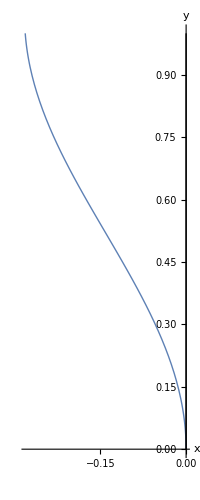

```mathematica
v1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

fact=0.2;
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,-fact*v[x]/.α->.999*αcr}],{x,0,l1},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef}]
```

### P_(cr,2)

```mathematica
Plot[detM[α], {α, 0, 7}, AxesLabel->{"α", "det(M)"}]
```

-Graphics-

```mathematica
αcr = α/.FindRoot[detM[α]==0, {α, 6}]
```

6.03677

```mathematica
Pcr = αcr^2*EJ1/l1^2/.EJ1->1
```

36.4425

```mathematica
Mcr = MM/.α->αcr//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 6.03677
0 | -24 | 0 | -149.395
0 | -36.4425 | 0 | 0)

```mathematica
Eigensystem[Mcr]//Chop
```

{{0.5+14.8238 ⅈ,0.5-14.8238 ⅈ,1.,0},{{0.00225477+0.0668485 ⅈ,0.0400904-0.0000816094 ⅈ,-0.992077,-0.00312012+0.0984523 ⅈ},{0.00225477-0.0668485 ⅈ,0.0400904+0.0000816094 ⅈ,-0.992077,-0.00312012-0.0984523 ⅈ},{1.,0,0,0},{-0.707107,0,0.707107,0}}}

```mathematica
{c1, c2, c3, c4} = Eigenvectors[Mcr]//Chop//Last
v[s]
```

{-0.707107,0,0.707107,0}

-0.707107+0.707107 Cos[s α]

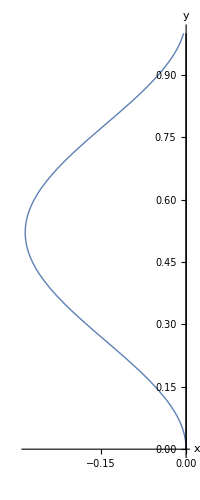

```mathematica
v1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

fact=0.2;
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,-fact*v[x]/.α->.999*αcr}],{x,0,l1},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef}]
```

### P_(cr,3)

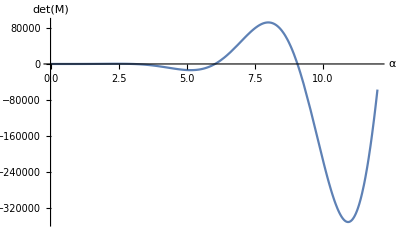

```mathematica
Plot[detM[α], {α, 0, 12}, AxesLabel->{"α", "det(M)"}]
```

```mathematica
αcr = α/.FindRoot[detM[α]==0, {α, 9}]
```

9.06368

```mathematica
Pcr = αcr^2*EJ1/l1^2/.EJ1->1
```

82.1503

```mathematica
Mcr = MM/.α->αcr//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 9.06368
0 | -24 | 0 | 232.524
0 | -82.1503 | 0 | 0)

```mathematica
Eigensystem[Mcr]//Chop
```

{{0.5+27.2825 ⅈ,0.5-27.2825 ⅈ,1.,0},{{-0.000666011-0.0363409 ⅈ,0.0385162-0.0027351 ⅈ,0.991803,0.00610815+0.116088 ⅈ},{-0.000666011+0.0363409 ⅈ,0.0385162+0.0027351 ⅈ,0.991803,0.00610815-0.116088 ⅈ},{1.,0,0,0},{-0.707107,0,0.707107,0}}}

```mathematica
{c1, c2, c3, c4} = Eigenvectors[Mcr]//Chop//Last
v[s]
```

{-0.707107,0,0.707107,0}

-0.707107+0.707107 Cos[s α]

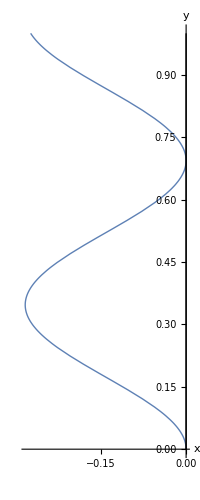

```mathematica
v1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

fact=0.2;
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,v1}][{x,-fact*v[x]/.α->.999*αcr}],{x,0,l1},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef}]
```

## Frame

```mathematica
ClearAll["Global`*"]

v1[s1_] = c1+c2*s1+c3*Cos[α1*s1]+c4*Sin[α1*s1];
v2[s2_] = c5+c6*s2+c7*s2^2+c8*s2^3;

(*
α1 = √(P1/EJ1);
α2 = √(P2/EJ2);
ϕ = k/(EJ1/l1)=(EJ2/l1)/(EJ1/l1)=EJ2/EJ1 ;
*)

EJ2 = 8;
EJ1 = 1;

ϕ = 3*EJ2/EJ1;

l1 = 1;
l2 = 2*l1;

{RR, MM} = CoefficientArrays[
{
v1[0] == 0, 
v1'[0]==0,
v2[l2/2]==0,
-(v2''[l2/2])==0,
v1'[l1]==v2'[0],
-(v1''[l1])==-EJ2/EJ1*v2''[0],
-(v1'''[l1]+α1^2*v1'[l1])==0,
v2[0]==0
},
{c1,c2,c3,c4,c5,c6,c7,c8}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | α1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | -2 | -6
0 | 1 | -α1 Sin[α1] | α1 Cos[α1] | 0 | -1 | 0 | 0
0 | 0 | α1^2 Cos[α1] | α1^2 Sin[α1] | 0 | 0 | 16 | 0
0 | -α1^2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(0
0
0
0
0
0
0
0)

```mathematica
detM[α1_, α2_] = Det[MM]//Simplify;
detM[α1, 0]
```

-4 α1^4 (α1 Cos[α1]+24 Sin[α1])

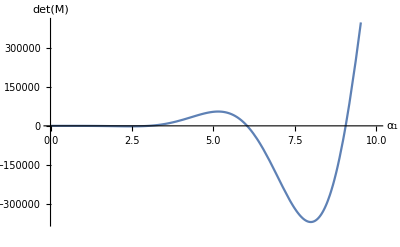

```mathematica
Plot[detM[α1, 0], {α1, 0, 10}, AxesLabel->{"α_1", "det(M)"}]
```

### P_(cr,1)

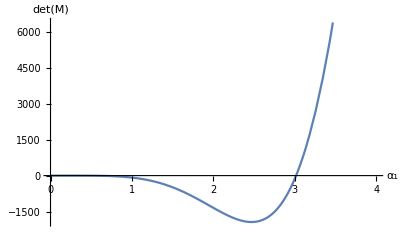

```mathematica
Plot[detM[α1, 0], {α1, 0, 4}, AxesLabel->{"α_1", "det(M)"}]
```

```mathematica
α1cr  = α1/.FindRoot[detM[α1, 0]==0, {α1, 3}]
```

3.01656

```mathematica
P1cr = α1cr^2*EJ1/l1^2/.EJ1->1
```

9.09962

```mathematica
Mcr = MM/.{α1->α1cr, α2->0};
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 3.01656 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | -2 | -6
0 | 1 | -0.376191 | -2.99301 | 0 | -1 | 0 | 0
0 | 0 | -9.02859 | 1.1348 | 0 | 0 | 16 | 0
0 | -9.09962 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
Eigensystem[Mcr]//Chop
```

{{-0.508575+4.20848 ⅈ,-0.508575-4.20848 ⅈ,-2.48058+3.09026 ⅈ,-2.48058-3.09026 ⅈ,3.48916+0.479545 ⅈ,3.48916-0.479545 ⅈ,1.,0},{{-0.0530611+0.0093287 ⅈ,0.0498659+0.00802621 ⅈ,0.040787-0.237379 ⅈ,-0.0361354+0.0655553 ⅈ,-0.000625785+0.18925 ⅈ,0.938811,-0.0042625+0.108336 ⅈ,0.0443392-0.00520949 ⅈ},{-0.0530611-0.0093287 ⅈ,0.0498659-0.00802621 ⅈ,0.040787+0.237379 ⅈ,-0.0361354-0.0655553 ⅈ,-0.000625785-0.18925 ⅈ,0.938811,-0.0042625-0.108336 ⅈ,0.0443392+0.00520949 ⅈ},{-0.00647084+0.0480898 ⅈ,-0.0298757+0.091373 ⅈ,-0.126088-0.187377 ⅈ,-0.0591341-0.136034 ⅈ,0.223503+0.0490486 ⅈ,0.900538,-0.206572+0.0778447 ⅈ,-0.0256541-0.0517323 ⅈ},{-0.00647084-0.0480898 ⅈ,-0.0298757-0.091373 ⅈ,-0.126088+0.187377 ⅈ,-0.0591341+0.136034 ⅈ,0.223503-0.0490486 ⅈ,0.900538,-0.206572-0.0778447 ⅈ,-0.0256541+0.0517323 ⅈ},{-0.101462+0.0214006 ⅈ,0.129271+0.0278983 ⅈ,-0.262817+0.00461406 ⅈ,0.102235+0.0435711 ⅈ,0.212887-0.0591361 ⅈ,-0.849006,-0.3407-0.0259327 ⅈ,0.0575966-0.0248646 ⅈ},{-0.101462-0.0214006 ⅈ,0.129271-0.0278983 ⅈ,-0.262817-0.00461406 ⅈ,0.102235-0.0435711 ⅈ,0.212887+0.0591361 ⅈ,-0.849006,-0.3407+0.0259327 ⅈ,0.0575966+0.0248646 ⅈ},{1.,0,0,0,0,0,0,0},{0.633048,0,-0.633048,0,0,0.238147,-0.357221,0.119074}}}

```mathematica
{c1,c2,c3,c4,c5,c6,c7,c8}=Eigenvectors[Mcr]//Chop//Last
v1[s1]
v2[s2]
```

{0.633048,0,-0.633048,0,0,0.238147,-0.357221,0.119074}

0.633048-0.633048 Cos[s1 α1]

0.238147 s2-0.357221 s2^2+0.119074 s2^3

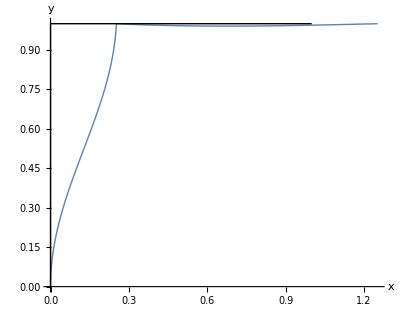

```mathematica
fact=0.2;

vv1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

vv2 = {0,l1};
vv2def = {fact*v1[l1], l1};
θ2 = 0;
T2 = RotationMatrix[θ2];


apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]],ParametricPlot[AffineTransform[{T2,vv2}][{x,0}],{x,0,l2/2},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,-fact*v1[x]/.α1->.999*α1cr}],{x,0,l1},PlotStyle->Thick],
ParametricPlot[AffineTransform[{T2,vv2def/.α1->.999α1cr}][{x,-fact*v2[x]}],{x,0,l2/2},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef},PlotRange->All]
```

### P_(cr,2)

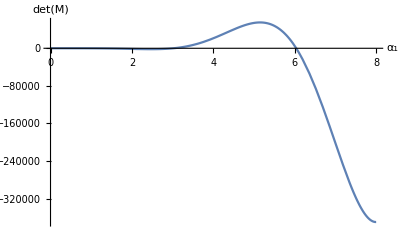

```mathematica
Plot[detM[α1, 0], {α1, 0, 8}, AxesLabel->{"α_1", "det(M)"}]
```

```mathematica
α1cr  = α1/.FindRoot[detM[α1, 0]==0, {α1, 6}]
```

6.03677

```mathematica
P1cr = α1cr^2*EJ1/l1^2/.EJ1->1
```

36.4425

```mathematica
Mcr = MM/.{α1->α1cr, α2->0};
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 6.03677 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | -2 | -6
0 | 1 | 1.47257 | 5.85441 | 0 | -1 | 0 | 0
0 | 0 | 35.3417 | -8.88956 | 0 | 0 | 16 | 0
0 | -36.4425 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
Eigensystem[Mcr]//Chop
```

{{-3.24977+6.26504 ⅈ,-3.24977-6.26504 ⅈ,6.93511+0.778759 ⅈ,6.93511-0.778759 ⅈ,-6.07813,1.,-0.292541,0},{{0.0153435-0.00178792 ⅈ,-0.0556367-0.105075 ⅈ,-0.0540052+0.103726 ⅈ,0.148215+0.01623 ⅈ,-0.0772873-0.192904 ⅈ,-0.72717,0.349334-0.504833 ⅈ,-0.0192201+0.022306 ⅈ},{0.0153435+0.00178792 ⅈ,-0.0556367+0.105075 ⅈ,-0.0540052-0.103726 ⅈ,0.148215-0.01623 ⅈ,-0.0772873+0.192904 ⅈ,-0.72717,0.349334+0.504833 ⅈ,-0.0192201-0.022306 ⅈ},{0.0221172-0.00411138 ⅈ,-0.020598-0.0128563 ⅈ,0.13447-0.00717748 ⅈ,-0.0185926-0.015297 ⅈ,-0.130594-0.00162635 ⅈ,0.972988,0.114382+0.0547128 ⅈ,-0.0186224+0.00185664 ⅈ},{0.0221172+0.00411138 ⅈ,-0.020598+0.0128563 ⅈ,0.13447+0.00717748 ⅈ,-0.0185926+0.015297 ⅈ,-0.130594+0.00162635 ⅈ,0.972988,0.114382-0.0547128 ⅈ,-0.0186224-0.00185664 ⅈ},{0.0278786,0.011117,-0.197329,-0.0130347,0.215302,0.952858,0.0666537,-0.0354223},{1.,0,0,0,0,0,0,0},{-0.255315,-0.00591428,0.330004,0.00126632,-0.0718619,0.466431,-0.736756,0.245647},{-0.322923,0,0.322923,0,0,0.475527,-0.713291,0.237764}}}

```mathematica
{c1,c2,c3,c4,c5,c6,c7,c8}=Eigenvectors[Mcr]//Chop//Last
v1[s1]
v2[s2]
```

{-0.322923,0,0.322923,0,0,0.475527,-0.713291,0.237764}

-0.322923+0.322923 Cos[s1 α1]

0.475527 s2-0.713291 s2^2+0.237764 s2^3

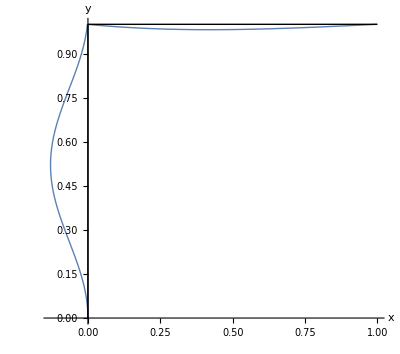

```mathematica
fact=0.2;

vv1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

vv2 = {0,l1};
vv2def = {fact*v1[l1], l1};
θ2 = 0;
T2 = RotationMatrix[θ2];


apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]],ParametricPlot[AffineTransform[{T2,vv2}][{x,0}],{x,0,l2/2},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,-fact*v1[x]/.α1->.999*α1cr}],{x,0,l1},PlotStyle->Thick],
ParametricPlot[AffineTransform[{T2,vv2def/.α1->.999α1cr}][{x,-fact*v2[x]}],{x,0,l2/2},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef},PlotRange->All]
```

### P_(cr,3)

```mathematica
Plot[detM[α1, 0], {α1, 0, 10}, AxesLabel->{"α_1", "det(M)"}]
```

-Graphics-

```mathematica
α1cr  = α1/.FindRoot[detM[α1, 0]==0, {α1, 9}]
```

9.06368

```mathematica
P1cr = α1cr^2*EJ1/l1^2/.EJ1->1
```

82.1503

```mathematica
Mcr = MM/.{α1->α1cr, α2->0};
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 9.06368 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | -2 | -6
0 | 1 | -3.20219 | -8.47917 | 0 | -1 | 0 | 0
0 | 0 | -76.8525 | 29.0236 | 0 | 0 | 16 | 0
0 | -82.1503 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
Eigensystem[Mcr]//Chop
```

{{11.823,-5.45266+9.76616 ⅈ,-5.45266-9.76616 ⅈ,-0.758951+9.25507 ⅈ,-0.758951-9.25507 ⅈ,1.60021,1.,0},{{0.00954593,-0.136262,0.103316,-0.162711,0.0593989,0.210283,0.946795,0.00502401},{-0.00437828+0.00391762 ⅈ,0.0152736+0.0475151 ⅈ,-0.0100086-0.0680381 ⅈ,-0.0620714-0.0173698 ⅈ,0.0474381+0.00928366 ⅈ,0.922966,-0.250017+0.268067 ⅈ,-0.00134281-0.00410767 ⅈ},{-0.00437828-0.00391762 ⅈ,0.0152736-0.0475151 ⅈ,-0.0100086+0.0680381 ⅈ,-0.0620714+0.0173698 ⅈ,0.0474381-0.00928366 ⅈ,0.922966,-0.250017-0.268067 ⅈ,-0.00134281+0.00410767 ⅈ},{-0.011662+0.00170281 ⅈ,0.00347721+0.00236814 ⅈ,0.00475321-0.110928 ⅈ,-0.00309296+0.00309105 ⅈ,0.0441224+0.101437 ⅈ,0.986779,-0.0183657+0.0323707 ⅈ,0.0104987-0.00562831 ⅈ},{-0.011662-0.00170281 ⅈ,0.00347721-0.00236814 ⅈ,0.00475321+0.110928 ⅈ,-0.00309296-0.00309105 ⅈ,0.0441224-0.101437 ⅈ,0.986779,-0.0183657-0.0323707 ⅈ,0.0104987+0.00562831 ⅈ},{-0.26927,0.0154543,-0.161619,0.00102342,0.422757,-0.152189,-0.793381,0.264187},{1.,0,0,0,0,0,0,0},{0.162459,0,-0.162459,0,0,0.520224,-0.780335,0.260112}}}

```mathematica
{c1,c2,c3,c4,c5,c6,c7,c8}=Eigenvectors[Mcr]//Chop//Last
v1[s1]
v2[s2]
```

{0.162459,0,-0.162459,0,0,0.520224,-0.780335,0.260112}

0.162459-0.162459 Cos[s1 α1]

0.520224 s2-0.780335 s2^2+0.260112 s2^3

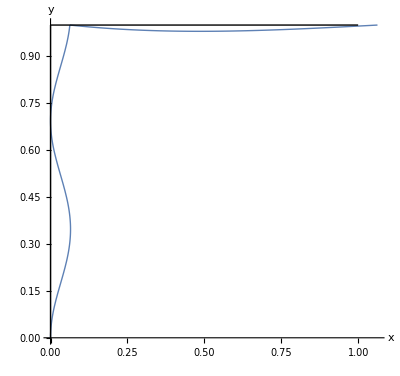

```mathematica
fact=0.2;

vv1 = {0,0};
θ1 = Pi/2;
T1 = RotationMatrix[θ1];

vv2 = {0,l1};
vv2def = {fact*v1[l1], l1};
θ2 = 0;
T2 = RotationMatrix[θ2];


apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
appv=Graphics[{Gray,Triangle[{{-1,-0.5},{0,0},{-1,0.5}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];

undef=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,0}],{x,0,l1},PlotStyle->Directive[Black,Thick]],ParametricPlot[AffineTransform[{T2,vv2}][{x,0}],{x,0,l2/2},PlotStyle->Directive[Black,Thick]]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

def=Show[{
ParametricPlot[AffineTransform[{T1,vv1}][{x,-fact*v1[x]/.α1->.999*α1cr}],{x,0,l1},PlotStyle->Thick],
ParametricPlot[AffineTransform[{T2,vv2def/.α1->.999α1cr}][{x,-fact*v2[x]}],{x,0,l2/2},PlotStyle->Thick]
},
AspectRatio->Automatic,AxesLabel->{x,y}];

Show[{def,undef},PlotRange->All]
```

# FEM solution

## Symmetric mode

## Frame

```mathematica
ClearAll["Global`*"];

EJ1 = 1;
EJ2 = 8;

EA1 = 10^10;
EA2 = 10^10;

l1 = 1;
l2 = 1*l1;

P1 = .;
P2 = 0;

θ1 = -Pi/2;
β=-θ1;
θ2 = 0;

ne1 = 20;
nn1 = ne1+1;

ne2 = 20;
nn2 = ne2;

ne = ne1+ne2;
nn = nn1+nn2;

coord1 = Table[{l1/ne1*(i1-1)*Cos[β], l1/ne1*(i1-1)*Sin[β]}, {i1, 1, nn1}];
coord2 = Table[{l2/ne2*(i2)*Cos[θ2],0}+{l1*Cos[β], l1*Sin[β]},{i2, 0,nn2}];

coord = Join[coord1, coord2];

ListPlot[{MapThread[Callout,{coord,Range[nn]}]},PlotRange->1.2*{{0,l1*Cos[β]+l2},{0,l1*Sin[β]}},PlotStyle->{Automatic,Red},Joined->True,PlotMarkers->Automatic,AspectRatio->Automatic,Axes->True]
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Callout,{{{0,0},{0,1/20},{0,1/10},{0,3/20},{0,1/5},{0,1/4},{0,3/10},{0,7/20},{0,2/5},{0,9/20},«32»},{1,2,3,4,5,6,7,8,9,10,«31»}}]; dimensions are 42 and 41.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Callout,{{{0.,0.},{0.,0.05},{0.,0.1},{0.,0.15},{0.,0.2},{0.,0.25},{0.,0.3},{0.,0.35},{0.,0.4},{0.,0.45},«32»},{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,«31»}}]; dimensions are 42 and 41.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

-Graphics-

```mathematica
Dimensions[Range[nn]]
Dimensions[coord]
```

{41}

{41,2}